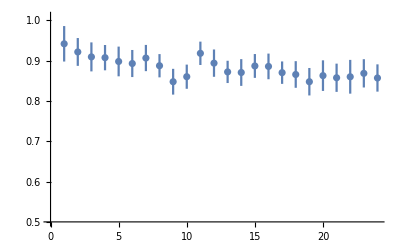

Max Degraded Starch={0.152014,0.0340821}

Mean Degraded Starch + SD={0.116815,0.0253204}

```mathematica
SetDirectory["~/Dropbox/work/PROJECTS/Artf Selection Melisa/Selection_Experiments/Selection_Nov15/RawData/Exp3_Bacillus/"];
dat=Import["Day17_NS.txt","Table"];
data=Table[dat[[i+4,j]],{i,1,8},{j,1,12}];
dum=0;
For[i=1,i<9,i++,For[z=0,z<4,z++,dum=dum+1;x[dum]=Table[data[[i,3z+k]],{k,1,3}];SD[dum]=StandardDeviation[x[dum]];G[dum]=Mean[x[dum]]];];
sta=Table[(G[dum]-0.04)/(G[26]-0.04),{dum,1,24}];
Ordering[sta,4];
sigma2=Table[SD[k]^2 (1/G[26])^2 +SD[26]^2 (G[k]/G[26]^2)^2,{k,1,24}];
sd=Table[√sigma2[[k]],{k,1,24}];
max=Sort[Table[{1-sta[[i]],sd[[i]]},{i,1,24}],#1[[1]]>#2[[1]]&][[1]];

Needs["ErrorBarPlots`"]
ErrorListPlot[Table[{sta[[i]],sd[[i]]},{i,1,24}],PlotRange->{0.5,1.01}]


Print["Max Degraded Starch=","",max]
Print["Mean Degraded Starch + SD=","",{1-Mean[sta],StandardDeviation[sta]}]
```